## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="G3PD2";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = False; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
Q10=10;


(* user will need to change this path *)
pathMASSef = "/home/mrama/Dropbox/MASSef/";
kineticDataFileName =  "kinetic_data.csv";

mainFolder = "fit_G3PD2_typeIII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Dropbox/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName,  assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological, Q10];
```

(glyc3p^c+nadp^c⇌dhap^c+h^c+nadph^c)^G3PD2

ordered bi bi; [nadp,glyc3p,dhap,nadph]

Structure:

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | glyc3p | nadp | 0.000099 | 0.00009405
0.00010395 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | nadph | 3.4×10^-6 | 3.23×10^-6
3.57×10^-6 |  | M | 7.4 | 23 | trishcl | 0.1 | 
1 | dhap | 0.00018 | 0.000171
0.000189 |  | M | 7.4 | 23 | trishcl | 0.1 | 
1 | nadp | 0.000165 | 0.00015675
0.00017325 |  | M | 7.4 | 23 | trishcl | 0.1 | 
1 | glyc3p | 0.00003 | 0.0000285
0.0000315 |  | M | 7.4 | 23 | trishcl | 0.1 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | glyc3p | 4.2×10^-6 | 3.99×10^-6
4.41×10^-6 | nadph | 0.0001 | Competitive | dhap | 0.00018 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | glyc3p | 6.5×10^-6 | 6.175×10^-6
6.825×10^-6 | dhap | 0.0001 | NonCompetitive | nadph | 3.4×10^-6 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | glyc3p | 2.5×10^-6 | 2.375×10^-6
2.625×10^-6 | dhap | 0.0001 | NonCompetitive | nadph | 3.4×10^-6 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | nadp | 0.0013 | 0.001235
0.001365 | nadph | 0.00001 | NonCompetitive | dhap | 0.00018 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | nadp | 0.0013 | 0.001235
0.001365 | nadph | 0.00001 | NonCompetitive | dhap | 0.00018 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kic | nadp | 0.000187 | 0.00017765
0.00019635 | dhap | 0.002 | Competitive | nadph | 3.4×10^-6 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kic | dhap | 0.000038 | 0.0000361
0.0000399 | nadp | 0.002 | Competitive | glyc3p | 0.00003 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | dhap | 0.00024 | 0.000228
0.000252 | glyc3p | 0.0001 | NonCompetitive | nadp | 0.000165 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | dhap | 0.00012 | 0.000114
0.000126 | glyc3p | 0.0001 | NonCompetitive | nadp | 0.000165 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | nadph | 8.×10^-7 | 7.6×10^-7
8.4×10^-7 | nadp | 0.0001 | NonCompetitive | glyc3p | 0.00003 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | nadph | 6.×10^-7 | 5.7×10^-7
6.3×10^-7 | nadp | 0.0001 | NonCompetitive | glyc3p | 0.00003 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kic | nadph | 4.×10^-7 | 3.8×10^-7
4.2×10^-7 | glyc3p | 0.0002 | Competitive | nadp | 0.000165 | M | 7.4 | 23 | trishcl | 0.1 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,1,1,1};
s05Priorities = Null;
kcatPriorities = Null;
inhibitionPriorities={1,1,1, 1,1,1,1,1,1,1,1,1};
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(glyc3p^c+nadp^c⇌dhap^c+h^c+nadph^c)^G3PD2

ordered bi bi; [nadp,glyc3p,dhap,nadph]

Structure:

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | glyc3p | nadp | 0.000099 | 0.00009405
0.00010395 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | nadph | 3.4×10^-6 | 3.23×10^-6
3.57×10^-6 |  | M | 7.4 | 23 | trishcl | 0.1 | 
1 | dhap | 0.00018 | 0.000171
0.000189 |  | M | 7.4 | 23 | trishcl | 0.1 | 
1 | nadp | 0.000165 | 0.00015675
0.00017325 |  | M | 7.4 | 23 | trishcl | 0.1 | 
1 | glyc3p | 0.00003 | 0.0000285
0.0000315 |  | M | 7.4 | 23 | trishcl | 0.1 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | glyc3p | 4.2×10^-6 | 3.99×10^-6
4.41×10^-6 | nadph | 0.0001 | Competitive | dhap | 0.00018 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | glyc3p | 6.5×10^-6 | 6.175×10^-6
6.825×10^-6 | dhap | 0.0001 | NonCompetitive | nadph | 3.4×10^-6 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | glyc3p | 2.5×10^-6 | 2.375×10^-6
2.625×10^-6 | dhap | 0.0001 | NonCompetitive | nadph | 3.4×10^-6 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | nadp | 0.0013 | 0.001235
0.001365 | nadph | 0.00001 | NonCompetitive | dhap | 0.00018 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | nadp | 0.0013 | 0.001235
0.001365 | nadph | 0.00001 | NonCompetitive | dhap | 0.00018 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kic | nadp | 0.000187 | 0.00017765
0.00019635 | dhap | 0.002 | Competitive | nadph | 3.4×10^-6 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kic | dhap | 0.000038 | 0.0000361
0.0000399 | nadp | 0.002 | Competitive | glyc3p | 0.00003 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | dhap | 0.00024 | 0.000228
0.000252 | glyc3p | 0.0001 | NonCompetitive | nadp | 0.000165 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | dhap | 0.00012 | 0.000114
0.000126 | glyc3p | 0.0001 | NonCompetitive | nadp | 0.000165 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | nadph | 8.×10^-7 | 7.6×10^-7
8.4×10^-7 | nadp | 0.0001 | NonCompetitive | glyc3p | 0.00003 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | nadph | 6.×10^-7 | 5.7×10^-7
6.3×10^-7 | nadp | 0.0001 | NonCompetitive | glyc3p | 0.00003 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kic | nadph | 4.×10^-7 | 3.8×10^-7
4.2×10^-7 | glyc3p | 0.0002 | Competitive | nadp | 0.000165 | M | 7.4 | 23 | trishcl | 0.1 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_G3PD2[c] + nadp[c] <=> E_G3PD2[c]&nadp",
				"E_G3PD2[c]&nadp + glyc3p[c] <=> E_G3PD2[c]&nadp&glyc3p",
				"E_G3PD2[c]&nadp&glyc3p <=> E_G3PD2[c]&nadph&dhap",
				"E_G3PD2[c]&nadph&dhap <=> E_G3PD2[c]&nadph + dhap[c]",
				"E_G3PD2[c]&nadph <=> E_G3PD2[c] + nadph[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites-> 0];
enzymeModel["Reactions"]
```

{((G3PD2^c)_^+nadp^c⇌(G3PD2^c&nadp^c)_^)^G3PD21,((G3PD2^c&nadph^c)_^⇌(G3PD2^c)_^+nadph^c)^G3PD22,((G3PD2^c&nadp^c)_^+glyc3p^c⇌(G3PD2^c&nadp^c&glyc3p^c)_^)^G3PD23,((G3PD2^c&nadph^c&dhap^c)_^⇌(G3PD2^c&nadph^c)_^+dhap^c)^G3PD24,((G3PD2^c&nadp^c&glyc3p^c)_^⇌(G3PD2^c&nadph^c&dhap^c)_^)^G3PD25}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((G3PD2^c)_^+nadp^c⇌(G3PD2^c&nadp^c)_^)^G3PD21,Overscript[(G3PD2^c&nadph^c)_^⇌(G3PD2^c)_^+nadph^c, G3PD22],((G3PD2^c&nadp^c)_^+glyc3p^c⇌(G3PD2^c&nadp^c&glyc3p^c)_^)^G3PD23,Overscript[(G3PD2^c&nadph^c&dhap^c)_^⇌(G3PD2^c&nadph^c)_^+dhap^c, G3PD24],((G3PD2^c&nadp^c&glyc3p^c)_^⇌(G3PD2^c&nadph^c&dhap^c)_^)^G3PD25};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=1;
assumedSaturatingConc = 1;
equivalentReactionsSetsList={};
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={{"prod_inhib_dhap", nadph^c->0},{ "prod_inhib_nadph", dhap^c->0}};
otherMetsForwardZeroSub={{"prod_inhib_glyc3p", nadp^c->0},{"prod_inhib_nadp", glyc3p^c->0}};
inhibitionListSubset=inhibitionList[[{2,3,8,9}]];
```

```mathematica
rxnMets =  Map[getID[#]&, Flatten[{getSubstrates[rxn], getProducts[rxn]}]];
	If[ !SameQ[inhibitionList, {}],
		inhibitors = inhibitionList[[All,3]];
		prodInhibBool = MemberQ[Map[MemberQ[rxnMets, #]&, inhibitors], True];,
		prodInhibBool = False;
	];

	{reverseZeroSub, forwardZeroSub, metSatForSub, metSatRevSub} = getMetsSub[rxn, assumedSaturatingConc];
	rates = getEnzymeRates[enzymeModel];
	{KeqName, KeqVal, volumeSub} = getMisc[enzymeModel, rxnName];
```

```mathematica
{allCatalyticReactions, nonCatalyticReactions} = classifyReactions[enzymeModel];
	
rateConstSubstitutionList = 
	If[TrueQ[MWCFlag],
		getUnifiedRateConstList[allCatalyticReactions, nonCatalyticReactions],
		{}
	];
```

```mathematica
If[ !SameQ[equivalentReactionsSetsList, {}] && !SameQ[equivalentReactionsSetsList, Null],
			AppendTo[rateConstSubstitutionList, getHalfHaldaneSub[equivalentReactionsSetsList]];
			rateConstSubstitutionList = Flatten @ rateConstSubstitutionList;
	];
```

```mathematica
(*Identify Transition Rate Equations*)
transitionID = getTransitionIDs[allCatalyticReactions];

(*Extract Transition Rate Equations*)
transitionRateEqs = getTransitionRateEqs[transitionID, rates];
```

```mathematica
(*King-Altman Workaround UsingMathematicaSolve*)
	(*This section of code will check to see if there is a 'absoluteFlux.m' file in the notebook directory from a previous cell evalution, and it will either derive a generalized flux equation (may take a long time) or import the previously derived flux equation. Note: If you modify the binding mechanism used in the constructEnzymeModule or manually add additional reactions to the model, you should delete the 'absoluteFlux.m' file in this notebook's current directory.*)
absoluteFluxNoProdInhib=
	If[prodInhibBool,
			Print["prod inhib"];
			getFluxEquation[inputPath, rxnName, enzymeModel, rateConstSubstitutionList, transitionRateEqs, simplifyFlag, simplifyMaxTime,nActiveSites, "NoProdInhibRefactor"],
			Null
	];
```

prod inhib

Generating flux equation...

{((G3PD2^c&nadp^c&glyc3p^c)_^-((G3PD2^c&nadph^c&dhap^c)_^)/K_G3PD25) Volume_c k_G3PD25^⟶}

Volume_c (-(G3PD2^c&nadph^c&dhap^c)_^ k_G3PD25^⟵+(G3PD2^c&nadp^c&glyc3p^c)_^ k_G3PD25^⟶)

Simplifying...

```mathematica
If[!SameQ[inhibitionListSubset,{}],
		{enzymeModel,nonCatalyticReactions} = addInhibitionReactions[enzymeModel,rxnName,inhibitionListSubset,allCatalyticReactions,nonCatalyticReactions];
];
```

```mathematica
absoluteFlux = getFluxEquation[inputPath, rxnName, enzymeModel, rateConstSubstitutionList, transitionRateEqs, simplifyFlag, simplifyMaxTime, nActiveSites, ""];
```

Generating flux equation...

{((G3PD2^c&nadp^c&glyc3p^c)_^-((G3PD2^c&nadph^c&dhap^c)_^)/K_G3PD25) Volume_c k_G3PD25^⟶}

Volume_c (-(G3PD2^c&nadph^c&dhap^c)_^ k_G3PD25^⟵+(G3PD2^c&nadp^c&glyc3p^c)_^ k_G3PD25^⟶)

Simplifying...

```mathematica
{absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, otherAbsoluteRatesForward, otherAbsoluteRatesReverse} = 
		getRateEqs[rxn, enzymeModel, absoluteFlux, rateConstSubstitutionList, reverseZeroSub, forwardZeroSub, volumeSub,
				metSatForSub, metSatRevSub, inputPath, absoluteFluxNoProdInhib, absoluteFluxNoProdInhib,
				otherMetsForwardZeroSub, otherMetsReverseZeroSub, simplifyFlag, simplifyMaxTime];
```

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating other relative rate forward equation...

Simplifying...

Generating other relative rate reverse equation...

Simplifying...

```mathematica
(* set up haldane relations *)
haldaneRatiosList  = Table[
				haldane = haldaneRelation[KeqName,catalyticReactionsSet]/.rateConstSubstitutionList;
				haldane[[2]],
		{catalyticReactionsSet, catalyticReactionsSetsList}] // DeleteDuplicates;
```

```mathematica
(*Assemble Rate Constant And Metabolite Substitutions for Export*)
{finalRateConsts,metsFull, metsSub, rateConstsSub} = 
			getMetRatesSubs[enzymeModel, haldaneRatiosList, absoluteRateForward, absoluteRateReverse, relativeRateForward, 
							relativeRateReverse,KeqVal,otherAbsoluteRatesForward, otherAbsoluteRatesReverse];
```

```mathematica
(*Export Equations*)
{eqnNameList, eqnValList, eqnValListPy, fileList, fileListSub} = 
		exportRateEqs[inputPath, absoluteRateForward, absoluteRateReverse, relativeRateForward, 
						relativeRateReverse, metsSub, metSatForSub, metSatRevSub, rateConstsSub,
						otherAbsoluteRatesForward, otherAbsoluteRatesReverse];
```

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList
, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, rateConstSubstitutionList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

```mathematica
FilePrint@dataPathList
```

Priority	dhap[c]	glyc3p[c]	nadp[c]	nadph[c]	param_G3PD2_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/haldaneRatio_1.txt"	0.000099
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/haldaneRatio_1.txt"	0.000099
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/haldaneRatio_1.txt"	0.000099
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/haldaneRatio_1.txt"	0.000099
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/haldaneRatio_1.txt"	0.000099
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/haldaneRatio_1.txt"	0.000099
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/haldaneRatio_1.txt"	0.000099
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/haldaneRatio_1.txt"	0.000099
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/haldaneRatio_1.txt"	0.000099
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/haldaneRatio_1.txt"	0.000099
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/haldaneRatio_1.txt"	0.000099
1	1	0	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_nadph.txt"	0.09090909090909097
1	1	0	0	5.388636854367791e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_nadph.txt"	0.1368068886032101
1	1	0	0	8.540413867132584e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_nadph.txt"	0.20076000891310194
1	1	0	0	1.3535643798818904e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_nadph.txt"	0.2847472489508014
1	1	0	0	2.1452549712326573e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_nadph.txt"	0.386863179846857
1	1	0	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_nadph.txt"	0.5000000000000001
1	1	0	0	5.388636854367791e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_nadph.txt"	0.6131368201531433
1	1	0	0	8.540413867132584e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_nadph.txt"	0.7152527510491989
1	1	0	0	0.000013535643798818902	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_nadph.txt"	0.7992399910868982
1	1	0	0	0.000021452549712326573	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_nadph.txt"	0.86319311139679
1	1	0	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_nadph.txt"	0.9090909090909091
1	0.000018000000000000017	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_dhap.txt"	0.09090909090909098
1	0.00002852807746430008	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_dhap.txt"	0.13680688860321016
1	0.00004521395576717252	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_dhap.txt"	0.200760008913102
1	0.00007165929069962952	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_dhap.txt"	0.28474724895080145
1	0.00011357232200643484	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_dhap.txt"	0.38686317984685703
1	0.00018000000000000017	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_dhap.txt"	0.5000000000000002
1	0.0002852807746430008	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_dhap.txt"	0.6131368201531433
1	0.0004521395576717252	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_dhap.txt"	0.7152527510491989
1	0.0007165929069962958	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_dhap.txt"	0.7992399910868984
1	0.0011357232200643484	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_dhap.txt"	0.86319311139679
1	0.0018000000000000017	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_dhap.txt"	0.9090909090909092
1	0	1	0.000016500000000000015	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_nadp.txt"	0.09090909090909097
1	0	1	0.000026150737675608408	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_nadp.txt"	0.13680688860321016
1	0	1	0.000041446126119908146	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_nadp.txt"	0.20076000891310203
1	0	1	0.00006568768314132706	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_nadp.txt"	0.2847472489508014
1	0	1	0.00010410796183923194	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_nadp.txt"	0.3868631798468571
1	0	1	0.00016500000000000016	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_nadp.txt"	0.5000000000000002
1	0	1	0.0002615073767560841	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_nadp.txt"	0.6131368201531434
1	0	1	0.0004144612611990815	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_nadp.txt"	0.7152527510491989
1	0	1	0.0006568768314132713	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_nadp.txt"	0.7992399910868985
1	0	1	0.0010410796183923194	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_nadp.txt"	0.8631931113967901
1	0	1	0.0016500000000000017	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_nadp.txt"	0.9090909090909092
1	0	3.0000000000000013e-6	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_glyc3p.txt"	0.09090909090909094
1	0	4.7546795773833446e-6	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_glyc3p.txt"	0.1368068886032101
1	0	7.535659294528749e-6	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_glyc3p.txt"	0.20076000891310194
1	0	0.000011943215116604912	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_glyc3p.txt"	0.28474724895080133
1	0	0.000018928720334405797	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_glyc3p.txt"	0.3868631798468569
1	0	0.00003000000000000001	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_glyc3p.txt"	0.5000000000000001
1	0	0.00004754679577383344	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_glyc3p.txt"	0.6131368201531432
1	0	0.00007535659294528749	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_glyc3p.txt"	0.7152527510491988
1	0	0.00011943215116604925	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_glyc3p.txt"	0.7992399910868984
1	0	0.00018928720334405796	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_glyc3p.txt"	0.86319311139679
1	0	0.00030000000000000014	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_glyc3p.txt"	0.9090909090909091
1	0.000018000000000000017	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.06250000000000006
1	0.000056920997883030876	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.17411239489546845
1	0.00018000000000000017	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.4000000000000002
1	0.0005692099788303088	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.6782688399674107
1	0.0018000000000000017	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.8695652173913044
1	0.000018000000000000017	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.047619047619047665
1	0.000056920997883030876	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.13652705949581442
1	0.00018000000000000017	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.33333333333333354
1	0.0005692099788303088	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.6125741132772071
1	0.0018000000000000017	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.8333333333333335
1	0.000018000000000000017	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.032258064516129066
1	0.000056920997883030876	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.09535767393826004
1	0.00018000000000000017	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.2500000000000002
1	0.0005692099788303088	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.5131670194948622
1	0.0018000000000000017	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.7692307692307694
1	0.0001	2.25e-6	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.04914933837429115
1	0.0001	2.25e-6	0	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.1359715179829786
1	0.0001	2.25e-6	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.3080568720379148
1	0.0001	2.25e-6	0	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.5136142175737065
1	0.0001	2.25e-6	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.6509764646970455
1	0.0001	4.5e-6	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.03367875647668395
1	0.0001	4.5e-6	0	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.09481652165128764
1	0.0001	4.5e-6	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.22260273972602748
1	0.0001	4.5e-6	0	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.3879359014999326
1	0.0001	4.5e-6	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.5070202808112324
1	0.0001	9.e-6	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.0206677265500795
1	0.0001	9.e-6	0	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.059062933642962216
1	0.0001	9.e-6	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.14317180616740097
1	0.0001	9.e-6	0	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.2604666499256048
1	0.0001	9.e-6	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.351541373715522
1	0.000018000000000000017	0	0.00065	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.06060606060606066
1	0.000056920997883030876	0	0.00065	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.16016871556802817
1	0.00018000000000000017	0	0.00065	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.3333333333333335
1	0.0005692099788303088	0	0.00065	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.5064979510986386
1	0.0018000000000000017	0	0.00065	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.6060606060606061
1	0.000018000000000000017	0	0.0013	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.04545454545454549
1	0.000056920997883030876	0	0.0013	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.12012653667602116
1	0.00018000000000000017	0	0.0013	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.2500000000000001
1	0.0005692099788303088	0	0.0013	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.379873463323979
1	0.0018000000000000017	0	0.0013	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.4545454545454546
1	0.000018000000000000017	0	0.0026	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.03030303030303033
1	0.000056920997883030876	0	0.0026	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.08008435778401408
1	0.00018000000000000017	0	0.0026	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.16666666666666674
1	0.0005692099788303088	0	0.0026	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.2532489755493193
1	0.0018000000000000017	0	0.0026	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.30303030303030304
1	0.002	0	0.0000935	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.06250000000000003
1	0.002	0	0.0000935	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.1741123948954684
1	0.002	0	0.0000935	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.40000000000000013
1	0.002	0	0.0000935	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.6782688399674105
1	0.002	0	0.0000935	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.8695652173913044
1	0.002	0	0.000187	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.047619047619047644
1	0.002	0	0.000187	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.1365270594958144
1	0.002	0	0.000187	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.3333333333333334
1	0.002	0	0.000187	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.612574113277207
1	0.002	0	0.000187	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.8333333333333334
1	0.002	0	0.000374	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.032258064516129045
1	0.002	0	0.000374	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.09535767393826002
1	0.002	0	0.000374	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.2500000000000001
1	0.002	0	0.000374	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.5131670194948621
1	0.002	0	0.000374	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.7692307692307694
1	0.000019	3.0000000000000013e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.06250000000000003
1	0.000019	9.486832980505141e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.17411239489546837
1	0.000019	0.00003000000000000001	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.40000000000000013
1	0.000019	0.00009486832980505142	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.6782688399674105
1	0.000019	0.00030000000000000014	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.8695652173913044
1	0.000038	3.0000000000000013e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.04761904761904764
1	0.000038	9.486832980505141e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.13652705949581434
1	0.000038	0.00003000000000000001	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.3333333333333334
1	0.000038	0.00009486832980505142	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.612574113277207
1	0.000038	0.00030000000000000014	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.8333333333333335
1	0.000076	3.0000000000000013e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.032258064516129045
1	0.000076	9.486832980505141e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.09535767393826
1	0.000076	0.00003000000000000001	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.25000000000000006
1	0.000076	0.00009486832980505142	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.5131670194948622
1	0.000076	0.00030000000000000014	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.7692307692307693
1	0.00009	0.0001	0.000016500000000000015	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.052980132450331174
1	0.00009	0.0001	0.000052177581392778313	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.1447390418373348
1	0.00009	0.0001	0.00016500000000000016	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.3200000000000002
1	0.00009	0.0001	0.0005217758139277831	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.518564992170751
1	0.00009	0.0001	0.0016500000000000017	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.6451612903225806
1	0.00018	0.0001	0.000016500000000000015	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.03738317757009349
1	0.00018	0.0001	0.000052177581392778313	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.10356583218373844
1	0.00018	0.0001	0.00016500000000000016	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.235294117647059
1	0.00018	0.0001	0.0005217758139277831	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.39361254767503817
1	0.00018	0.0001	0.0016500000000000017	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.5000000000000001
1	0.00036	0.0001	0.000016500000000000015	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.023529411764705903
1	0.00036	0.0001	0.000052177581392778313	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.06601047571169773
1	0.00036	0.0001	0.00016500000000000016	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.1538461538461539
1	0.00036	0.0001	0.0005217758139277831	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.26561052385648354
1	0.00036	0.0001	0.0016500000000000017	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.3448275862068966
1	0	3.0000000000000013e-6	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.057901085645355864
1	0	9.486832980505141e-6	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.15517252975139625
1	0	0.00003000000000000001	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.33103448275862074
1	0	0.00009486832980505142	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.5159442342521813
1	0	0.00030000000000000014	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.6266318537859008
1	0	3.0000000000000013e-6	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.042477876106194704
1	0	9.486832980505141e-6	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.11459214550830052
1	0	0.00003000000000000001	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.2474226804123712
1	0	0.00009486832980505142	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.39060056309756436
1	0	0.00030000000000000014	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.47808764940239046
1	0	3.0000000000000013e-6	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.02771362586605082
1	0	9.486832980505141e-6	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.07523930500173176
1	0	0.00003000000000000001	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.16438356164383564
1	0	0.00009486832980505142	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.2628747818212248
1	0	0.00030000000000000014	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.32432432432432434
1	0	0.0002	0.000016500000000000015	2.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.06250000000000006
1	0	0.0002	0.000052177581392778313	2.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.17411239489546848
1	0	0.0002	0.00016500000000000016	2.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.4000000000000002
1	0	0.0002	0.0005217758139277831	2.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.6782688399674106
1	0	0.0002	0.0016500000000000017	2.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.8695652173913045
1	0	0.0002	0.000016500000000000015	4.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.047619047619047665
1	0	0.0002	0.000052177581392778313	4.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.13652705949581445
1	0	0.0002	0.00016500000000000016	4.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.33333333333333354
1	0	0.0002	0.0005217758139277831	4.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.6125741132772071
1	0	0.0002	0.0016500000000000017	4.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.8333333333333335
1	0	0.0002	0.000016500000000000015	8.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.03225806451612906
1	0	0.0002	0.000052177581392778313	8.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.09535767393826007
1	0	0.0002	0.00016500000000000016	8.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.25000000000000017
1	0	0.0002	0.0005217758139277831	8.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.5131670194948623
1	0	0.0002	0.0016500000000000017	8.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.7692307692307693

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName, fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, rateConstSubstitutionList,  customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	dhap[c]	glyc3p[c]	nadp[c]	nadph[c]	param_G3PD2_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/haldaneRatio_1.txt"	0.000096483739260425
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/haldaneRatio_1.txt"	0.000096483739260425
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/haldaneRatio_1.txt"	0.000096483739260425
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/haldaneRatio_1.txt"	0.000096483739260425
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/haldaneRatio_1.txt"	0.000096483739260425
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/haldaneRatio_1.txt"	0.000096483739260425
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/haldaneRatio_1.txt"	0.000096483739260425
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/haldaneRatio_1.txt"	0.000096483739260425
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/haldaneRatio_1.txt"	0.000096483739260425
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/haldaneRatio_1.txt"	0.000096483739260425
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/haldaneRatio_1.txt"	0.000096483739260425
1	1	0	0	3.129037597873447e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_nadph.txt"	0.09090909090909094
1	1	0	0	4.959190387824503e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_nadph.txt"	0.13680688860321008
1	1	0	0	7.859787085781648e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_nadph.txt"	0.20076000891310197
1	1	0	0	1.2456923046449087e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_nadph.txt"	0.28474724895080133
1	1	0	0	1.9742892535329122e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_nadph.txt"	0.386863179846857
1	1	0	0	3.129037597873447e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_nadph.txt"	0.5000000000000001
1	1	0	0	4.959190387824503e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_nadph.txt"	0.6131368201531433
1	1	0	0	7.859787085781647e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_nadph.txt"	0.7152527510491989
1	1	0	0	0.000012456923046449087	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_nadph.txt"	0.7992399910868981
1	1	0	0	0.00001974289253532912	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_nadph.txt"	0.8631931113967899
1	1	0	0	0.000031290375978734474	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_nadph.txt"	0.9090909090909092
1	0.000020410217358979325	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_dhap.txt"	0.09090909090909095
1	0.00003234801454889799	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_dhap.txt"	0.1368068886032101
1	0.0000512681480481815	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_dhap.txt"	0.20076000891310194
1	0.00008125453883165142	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_dhap.txt"	0.2847472489508017
1	0.0001287797654508513	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_dhap.txt"	0.386863179846857
1	0.00020410217358979323	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_dhap.txt"	0.5000000000000001
1	0.0003234801454889799	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_dhap.txt"	0.6131368201531432
1	0.000512681480481815	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_dhap.txt"	0.7152527510491988
1	0.0008125453883165134	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_dhap.txt"	0.7992399910868985
1	0.0012877976545085132	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_dhap.txt"	0.86319311139679
1	0.0020410217358979325	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_dhap.txt"	0.9090909090909092
1	0	1	0.000015596983927693493	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_nadp.txt"	0.0909090909090909
1	0	1	0.000024719553649926826	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_nadp.txt"	0.13680688860321003
1	0	1	0.00003917785230044631	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_nadp.txt"	0.20076000891310186
1	0	1	0.00006209271140622423	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_nadp.txt"	0.2847472489508012
1	0	1	0.00009841031560917736	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_nadp.txt"	0.3868631798468568
1	0	1	0.00015596983927693492	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_nadp.txt"	0.4999999999999999
1	0	1	0.00024719553649926826	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_nadp.txt"	0.6131368201531431
1	0	1	0.0003917785230044631	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_nadp.txt"	0.7152527510491987
1	0	1	0.000620927114062243	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_nadp.txt"	0.7992399910868982
1	0	1	0.0009841031560917737	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_nadp.txt"	0.8631931113967899
1	0	1	0.0015596983927693491	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_nadp.txt"	0.9090909090909091
1	0	3.0156248333855526e-6	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_glyc3p.txt"	0.09090909090909087
1	0	4.779443269449444e-6	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_glyc3p.txt"	0.13680688860321
1	0	7.574907101504514e-6	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_glyc3p.txt"	0.20076000891310183
1	0	0.000012005418698699829	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_glyc3p.txt"	0.28474724895080117
1	0	0.00001902730636821473	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_glyc3p.txt"	0.38686317984685675
1	0	0.000030156248333855528	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_glyc3p.txt"	0.49999999999999983
1	0	0.00004779443269449444	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_glyc3p.txt"	0.6131368201531431
1	0	0.00007574907101504515	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_glyc3p.txt"	0.7152527510491987
1	0	0.00012005418698699842	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_glyc3p.txt"	0.7992399910868981
1	0	0.00019027306368214728	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_glyc3p.txt"	0.8631931113967898
1	0	0.0003015624833385553	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_glyc3p.txt"	0.9090909090909091
1	0.000018000000000000017	2.1037538999529466e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.06250000000000006
1	0.000056920997883030876	2.1037538999529466e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.17411239489546845
1	0.00018000000000000017	2.1037538999529466e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.4000000000000002
1	0.0005692099788303088	2.1037538999529466e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.6782688399674107
1	0.0018000000000000017	2.1037538999529466e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.8695652173913044
1	0.000018000000000000017	4.207507799905893e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.047619047619047665
1	0.000056920997883030876	4.207507799905893e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.13652705949581442
1	0.00018000000000000017	4.207507799905893e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.33333333333333354
1	0.0005692099788303088	4.207507799905893e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.6125741132772071
1	0.0018000000000000017	4.207507799905893e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.8333333333333335
1	0.000018000000000000017	8.415015599811786e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.032258064516129066
1	0.000056920997883030876	8.415015599811786e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.09535767393826004
1	0.00018000000000000017	8.415015599811786e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.2500000000000002
1	0.0005692099788303088	8.415015599811786e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.5131670194948622
1	0.0018000000000000017	8.415015599811786e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.7692307692307694
1	0.0001	2.323100334937473e-6	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.04836455105829019
1	0.0001	2.323100334937473e-6	0	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.13412625445262563
1	0.0001	2.323100334937473e-6	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.30535015151655454
1	0.0001	2.323100334937473e-6	0	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.5120681925411658
1	0.0001	2.323100334937473e-6	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.6515542596641035
1	0.0001	4.646200669874946e-6	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.03294610527941429
1	0.0001	4.646200669874946e-6	0	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.09303151126927353
1	0.0001	4.646200669874946e-6	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.2197871000642933
1	0.0001	4.646200669874946e-6	0	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.38617463369541344
1	0.0001	4.646200669874946e-6	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.5077216373944418
1	0.0001	9.292401339749893e-6	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.020118618276724343
1	0.0001	9.292401339749893e-6	0	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.057684050662945886
1	0.0001	9.292401339749893e-6	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.14085072169558133
1	0.0001	9.292401339749893e-6	0	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.2588811572461585
1	0.0001	9.292401339749893e-6	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.35221606247258225
1	0.000018000000000000017	0	0.0006418803472088958	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.060700691713789376
1	0.000056920997883030876	0	0.0006418803472088958	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.16032676902440174
1	0.00018000000000000017	0	0.0006418803472088958	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.33332965124202485
1	0.0005692099788303088	0	0.0006418803472088958	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.5059879589805726
1	0.0018000000000000017	0	0.0006418803472088958	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.6051038933232198
1	0.000018000000000000017	0	0.0012837606944177916	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.04556108862970446
1	0.000056920997883030876	0	0.0012837606944177916	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.12030443458869829
1	0.00018000000000000017	0	0.0012837606944177916	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.2499958576701565
1	0.0005692099788303088	0	0.0012837606944177916	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.379300010895401
1	0.0018000000000000017	0	0.0012837606944177916	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.45347000155804146
1	0.000018000000000000017	0	0.002567521388835583	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.030397809400099635
1	0.000056920997883030876	0	0.002567521388835583	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.08024256736057825
1	0.00018000000000000017	0	0.002567521388835583	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.166662984616031
1	0.0005692099788303088	0	0.002567521388835583	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.2527394964251104
1	0.0018000000000000017	0	0.002567521388835583	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.30207509815642164
1	0.002	0	0.00009610879322718565	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.06250000000000003
1	0.002	0	0.00009610879322718565	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.1741123948954684
1	0.002	0	0.00009610879322718565	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.40000000000000013
1	0.002	0	0.00009610879322718565	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.6782688399674105
1	0.002	0	0.00009610879322718565	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.8695652173913044
1	0.002	0	0.0001922175864543713	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.047619047619047644
1	0.002	0	0.0001922175864543713	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.1365270594958144
1	0.002	0	0.0001922175864543713	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.3333333333333334
1	0.002	0	0.0001922175864543713	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.612574113277207
1	0.002	0	0.0001922175864543713	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.8333333333333334
1	0.002	0	0.0003844351729087426	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.032258064516129045
1	0.002	0	0.0003844351729087426	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.09535767393826002
1	0.002	0	0.0003844351729087426	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.2500000000000001
1	0.002	0	0.0003844351729087426	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.5131670194948621
1	0.002	0	0.0003844351729087426	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.7692307692307694
1	0.00001900948058623012	3.0000000000000013e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.06250000000000003
1	0.00001900948058623012	9.486832980505141e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.17411239489546837
1	0.00001900948058623012	0.00003000000000000001	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.40000000000000013
1	0.00001900948058623012	0.00009486832980505142	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.6782688399674105
1	0.00001900948058623012	0.00030000000000000014	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.8695652173913044
1	0.00003801896117246024	3.0000000000000013e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.04761904761904764
1	0.00003801896117246024	9.486832980505141e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.13652705949581434
1	0.00003801896117246024	0.00003000000000000001	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.3333333333333334
1	0.00003801896117246024	0.00009486832980505142	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.612574113277207
1	0.00003801896117246024	0.00030000000000000014	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.8333333333333335
1	0.00007603792234492048	3.0000000000000013e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.032258064516129045
1	0.00007603792234492048	9.486832980505141e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.09535767393826
1	0.00007603792234492048	0.00003000000000000001	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.25000000000000006
1	0.00007603792234492048	0.00009486832980505142	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.5131670194948622
1	0.00007603792234492048	0.00030000000000000014	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.7692307692307693
1	0.00008801172619308182	0.0001	0.000016500000000000015	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.05392826850725052
1	0.00008801172619308182	0.0001	0.000052177581392778313	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.1468363738317205
1	0.00008801172619308182	0.0001	0.00016500000000000016	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.3225755387735473
1	0.00008801172619308182	0.0001	0.0005217758139277831	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.5190048718043427
1	0.00008801172619308182	0.0001	0.0016500000000000017	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.6427813699588212
1	0.00017602345238616364	0.0001	0.000016500000000000015	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.038334296563139955
1	0.00017602345238616364	0.0001	0.000052177581392778313	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.10572695809169022
1	0.00017602345238616364	0.0001	0.00016500000000000016	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.23808967437456838
1	0.00017602345238616364	0.0001	0.0005217758139277831	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.3941196390597012
1	0.00017602345238616364	0.0001	0.0016500000000000017	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.49714690924781946
1	0.0003520469047723273	0.0001	0.000016500000000000015	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.024287996139776148
1	0.0003520469047723273	0.0001	0.000052177581392778313	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.06777651318297108
1	0.0003520469047723273	0.0001	0.00016500000000000016	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.15624520784590168
1	0.0003520469047723273	0.0001	0.0005217758139277831	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.26607254788615603
1	0.0003520469047723273	0.0001	0.0016500000000000017	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.34211944939784794
1	0	3.0000000000000013e-6	0.0001	3.4658817516561726e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.058215630659585585
1	0	9.486832980505141e-6	0.0001	3.4658817516561726e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.1557909715555081
1	0	0.00003000000000000001	0.0001	3.4658817516561726e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.331491327638692
1	0	0.00009486832980505142	0.0001	3.4658817516561726e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.5152503366919886
1	0	0.00030000000000000014	0.0001	3.4658817516561726e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.6247713872558774
1	0	3.0000000000000013e-6	0.0001	6.931763503312345e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.042817320600216896
1	0	9.486832980505141e-6	0.0001	6.931763503312345e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.11526797199910761
1	0	0.00003000000000000001	0.0001	6.931763503312345e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.24793345347921777
1	0	0.00009486832980505142	0.0001	6.931763503312345e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.38980571274173864
1	0	0.00030000000000000014	0.0001	6.931763503312345e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.47592510815726297
1	0	3.0000000000000013e-6	0.0001	1.386352700662469e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.028003306287614074
1	0	9.486832980505141e-6	0.0001	1.386352700662469e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.07582308326398883
1	0	0.00003000000000000001	0.0001	1.386352700662469e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.16483478398700885
1	0	0.00009486832980505142	0.0001	1.386352700662469e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.2621552635757265
1	0	0.00030000000000000014	0.0001	1.386352700662469e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.32233714013317194
1	0	0.0002	0.000016500000000000015	2.1280015897898585e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.06250000000000006
1	0	0.0002	0.000052177581392778313	2.1280015897898585e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.17411239489546848
1	0	0.0002	0.00016500000000000016	2.1280015897898585e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.4000000000000002
1	0	0.0002	0.0005217758139277831	2.1280015897898585e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.6782688399674106
1	0	0.0002	0.0016500000000000017	2.1280015897898585e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.8695652173913045
1	0	0.0002	0.000016500000000000015	4.256003179579717e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.047619047619047665
1	0	0.0002	0.000052177581392778313	4.256003179579717e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.13652705949581445
1	0	0.0002	0.00016500000000000016	4.256003179579717e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.33333333333333354
1	0	0.0002	0.0005217758139277831	4.256003179579717e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.6125741132772071
1	0	0.0002	0.0016500000000000017	4.256003179579717e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.8333333333333335
1	0	0.0002	0.000016500000000000015	8.512006359159434e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.03225806451612906
1	0	0.0002	0.000052177581392778313	8.512006359159434e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.09535767393826007
1	0	0.0002	0.00016500000000000016	8.512006359159434e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.25000000000000017
1	0	0.0002	0.0005217758139277831	8.512006359159434e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.5131670194948623
1	0	0.0002	0.0016500000000000017	8.512006359159434e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.7692307692307693

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"Keq",1,{0.01,0.1,100}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, rateConstSubstitutionList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

```mathematica
FilePrint[dataPathList[[8]]]
```

Priority	dhap[c]	glyc3p[c]	nadp[c]	nadph[c]	param_G3PD2_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/haldaneRatio_1.txt"	0.000099
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/haldaneRatio_1.txt"	0.000099
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/haldaneRatio_1.txt"	0.000099
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/haldaneRatio_1.txt"	0.000099
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/haldaneRatio_1.txt"	0.000099
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/haldaneRatio_1.txt"	0.000099
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/haldaneRatio_1.txt"	0.000099
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/haldaneRatio_1.txt"	0.000099
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/haldaneRatio_1.txt"	0.000099
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/haldaneRatio_1.txt"	0.000099
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/haldaneRatio_1.txt"	0.000099
1	1	0	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_nadph.txt"	0.09090909090909097
1	1	0	0	5.388636854367791e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_nadph.txt"	0.1368068886032101
1	1	0	0	8.540413867132584e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_nadph.txt"	0.20076000891310194
1	1	0	0	1.3535643798818904e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_nadph.txt"	0.2847472489508014
1	1	0	0	2.1452549712326573e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_nadph.txt"	0.386863179846857
1	1	0	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_nadph.txt"	0.5000000000000001
1	1	0	0	5.388636854367791e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_nadph.txt"	0.6131368201531433
1	1	0	0	8.540413867132584e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_nadph.txt"	0.7152527510491989
1	1	0	0	0.000013535643798818902	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_nadph.txt"	0.7992399910868982
1	1	0	0	0.000021452549712326573	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_nadph.txt"	0.86319311139679
1	1	0	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_nadph.txt"	0.9090909090909091
1	0.000018000000000000017	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_dhap.txt"	0.09090909090909098
1	0.00002852807746430008	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_dhap.txt"	0.13680688860321016
1	0.00004521395576717252	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_dhap.txt"	0.200760008913102
1	0.00007165929069962952	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_dhap.txt"	0.28474724895080145
1	0.00011357232200643484	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_dhap.txt"	0.38686317984685703
1	0.00018000000000000017	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_dhap.txt"	0.5000000000000002
1	0.0002852807746430008	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_dhap.txt"	0.6131368201531433
1	0.0004521395576717252	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_dhap.txt"	0.7152527510491989
1	0.0007165929069962958	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_dhap.txt"	0.7992399910868984
1	0.0011357232200643484	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_dhap.txt"	0.86319311139679
1	0.0018000000000000017	0	0	1	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_dhap.txt"	0.9090909090909092
1	0	1	1.	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_nadp.txt"	0.09090909090909091
1	0	1	1.5848931924611136	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_nadp.txt"	0.13680688860321003
1	0	1	2.51188643150958	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_nadp.txt"	0.20076000891310172
1	0	1	3.981071705534973	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_nadp.txt"	0.2847472489508015
1	0	1	6.309573444801933	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_nadp.txt"	0.386863179846857
1	0	1	10.	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_nadp.txt"	0.5
1	0	1	15.848931924611142	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_nadp.txt"	0.6131368201531431
1	0	1	25.11886431509581	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_nadp.txt"	0.7152527510491987
1	0	1	39.810717055349734	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_nadp.txt"	0.7992399910868984
1	0	1	63.09573444801933	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_nadp.txt"	0.86319311139679
1	0	1	100.	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_nadp.txt"	0.9090909090909091
1	0	3.0000000000000013e-6	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_glyc3p.txt"	0.09090909090909094
1	0	4.7546795773833446e-6	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_glyc3p.txt"	0.1368068886032101
1	0	7.535659294528749e-6	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_glyc3p.txt"	0.20076000891310194
1	0	0.000011943215116604912	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_glyc3p.txt"	0.28474724895080133
1	0	0.000018928720334405797	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_glyc3p.txt"	0.3868631798468569
1	0	0.00003000000000000001	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_glyc3p.txt"	0.5000000000000001
1	0	0.00004754679577383344	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_glyc3p.txt"	0.6131368201531432
1	0	0.00007535659294528749	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_glyc3p.txt"	0.7152527510491988
1	0	0.00011943215116604925	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_glyc3p.txt"	0.7992399910868984
1	0	0.00018928720334405796	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_glyc3p.txt"	0.86319311139679
1	0	0.00030000000000000014	1	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_glyc3p.txt"	0.9090909090909091
1	0.000018000000000000017	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.06250000000000006
1	0.000056920997883030876	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.17411239489546845
1	0.00018000000000000017	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.4000000000000002
1	0.0005692099788303088	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.6782688399674107
1	0.0018000000000000017	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.8695652173913044
1	0.000018000000000000017	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.047619047619047665
1	0.000056920997883030876	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.13652705949581442
1	0.00018000000000000017	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.33333333333333354
1	0.0005692099788303088	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.6125741132772071
1	0.0018000000000000017	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.8333333333333335
1	0.000018000000000000017	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.032258064516129066
1	0.000056920997883030876	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.09535767393826004
1	0.00018000000000000017	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.2500000000000002
1	0.0005692099788303088	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.5131670194948622
1	0.0018000000000000017	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.7692307692307694
1	0.0001	2.25e-6	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.04914933837429115
1	0.0001	2.25e-6	0	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.1359715179829786
1	0.0001	2.25e-6	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.3080568720379148
1	0.0001	2.25e-6	0	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.5136142175737065
1	0.0001	2.25e-6	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.6509764646970455
1	0.0001	4.5e-6	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.03367875647668395
1	0.0001	4.5e-6	0	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.09481652165128764
1	0.0001	4.5e-6	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.22260273972602748
1	0.0001	4.5e-6	0	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.3879359014999326
1	0.0001	4.5e-6	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.5070202808112324
1	0.0001	9.e-6	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.0206677265500795
1	0.0001	9.e-6	0	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.059062933642962216
1	0.0001	9.e-6	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.14317180616740097
1	0.0001	9.e-6	0	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.2604666499256048
1	0.0001	9.e-6	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.351541373715522
1	0.000018000000000000017	0	0.00065	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.06060606060606066
1	0.000056920997883030876	0	0.00065	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.16016871556802817
1	0.00018000000000000017	0	0.00065	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.3333333333333335
1	0.0005692099788303088	0	0.00065	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.5064979510986386
1	0.0018000000000000017	0	0.00065	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.6060606060606061
1	0.000018000000000000017	0	0.0013	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.04545454545454549
1	0.000056920997883030876	0	0.0013	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.12012653667602116
1	0.00018000000000000017	0	0.0013	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.2500000000000001
1	0.0005692099788303088	0	0.0013	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.379873463323979
1	0.0018000000000000017	0	0.0013	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.4545454545454546
1	0.000018000000000000017	0	0.0026	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.03030303030303033
1	0.000056920997883030876	0	0.0026	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.08008435778401408
1	0.00018000000000000017	0	0.0026	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.16666666666666674
1	0.0005692099788303088	0	0.0026	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.2532489755493193
1	0.0018000000000000017	0	0.0026	0.00001	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.30303030303030304
1	0.002	0	0.0000935	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.06250000000000003
1	0.002	0	0.0000935	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.1741123948954684
1	0.002	0	0.0000935	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.40000000000000013
1	0.002	0	0.0000935	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.6782688399674105
1	0.002	0	0.0000935	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.8695652173913044
1	0.002	0	0.000187	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.047619047619047644
1	0.002	0	0.000187	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.1365270594958144
1	0.002	0	0.000187	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.3333333333333334
1	0.002	0	0.000187	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.612574113277207
1	0.002	0	0.000187	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.8333333333333334
1	0.002	0	0.000374	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.032258064516129045
1	0.002	0	0.000374	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.09535767393826002
1	0.002	0	0.000374	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.2500000000000001
1	0.002	0	0.000374	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.5131670194948621
1	0.002	0	0.000374	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.7692307692307694
1	0.000019	3.0000000000000013e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.06250000000000003
1	0.000019	9.486832980505141e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.17411239489546837
1	0.000019	0.00003000000000000001	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.40000000000000013
1	0.000019	0.00009486832980505142	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.6782688399674105
1	0.000019	0.00030000000000000014	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.8695652173913044
1	0.000038	3.0000000000000013e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.04761904761904764
1	0.000038	9.486832980505141e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.13652705949581434
1	0.000038	0.00003000000000000001	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.3333333333333334
1	0.000038	0.00009486832980505142	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.612574113277207
1	0.000038	0.00030000000000000014	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.8333333333333335
1	0.000076	3.0000000000000013e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.032258064516129045
1	0.000076	9.486832980505141e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.09535767393826
1	0.000076	0.00003000000000000001	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.25000000000000006
1	0.000076	0.00009486832980505142	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.5131670194948622
1	0.000076	0.00030000000000000014	0.002	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.7692307692307693
1	0.00009	0.0001	0.000016500000000000015	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.052980132450331174
1	0.00009	0.0001	0.000052177581392778313	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.1447390418373348
1	0.00009	0.0001	0.00016500000000000016	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.3200000000000002
1	0.00009	0.0001	0.0005217758139277831	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.518564992170751
1	0.00009	0.0001	0.0016500000000000017	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.6451612903225806
1	0.00018	0.0001	0.000016500000000000015	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.03738317757009349
1	0.00018	0.0001	0.000052177581392778313	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.10356583218373844
1	0.00018	0.0001	0.00016500000000000016	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.235294117647059
1	0.00018	0.0001	0.0005217758139277831	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.39361254767503817
1	0.00018	0.0001	0.0016500000000000017	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.5000000000000001
1	0.00036	0.0001	0.000016500000000000015	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.023529411764705903
1	0.00036	0.0001	0.000052177581392778313	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.06601047571169773
1	0.00036	0.0001	0.00016500000000000016	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.1538461538461539
1	0.00036	0.0001	0.0005217758139277831	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.26561052385648354
1	0.00036	0.0001	0.0016500000000000017	0	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.3448275862068966
1	0	3.0000000000000013e-6	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.057901085645355864
1	0	9.486832980505141e-6	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.15517252975139625
1	0	0.00003000000000000001	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.33103448275862074
1	0	0.00009486832980505142	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.5159442342521813
1	0	0.00030000000000000014	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.6266318537859008
1	0	3.0000000000000013e-6	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.042477876106194704
1	0	9.486832980505141e-6	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.11459214550830052
1	0	0.00003000000000000001	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.2474226804123712
1	0	0.00009486832980505142	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.39060056309756436
1	0	0.00030000000000000014	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.47808764940239046
1	0	3.0000000000000013e-6	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.02771362586605082
1	0	9.486832980505141e-6	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.07523930500173176
1	0	0.00003000000000000001	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.16438356164383564
1	0	0.00009486832980505142	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.2628747818212248
1	0	0.00030000000000000014	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.32432432432432434
1	0	0.0002	0.000016500000000000015	2.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.06250000000000006
1	0	0.0002	0.000052177581392778313	2.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.17411239489546848
1	0	0.0002	0.00016500000000000016	2.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.4000000000000002
1	0	0.0002	0.0005217758139277831	2.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.6782688399674106
1	0	0.0002	0.0016500000000000017	2.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.8695652173913045
1	0	0.0002	0.000016500000000000015	4.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.047619047619047665
1	0	0.0002	0.000052177581392778313	4.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.13652705949581445
1	0	0.0002	0.00016500000000000016	4.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.33333333333333354
1	0	0.0002	0.0005217758139277831	4.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.6125741132772071
1	0	0.0002	0.0016500000000000017	4.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.8333333333333335
1	0	0.0002	0.000016500000000000015	8.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.03225806451612906
1	0	0.0002	0.000052177581392778313	8.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.09535767393826007
1	0	0.0002	0.00016500000000000016	8.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.25000000000000017
1	0	0.0002	0.0005217758139277831	8.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.5131670194948623
1	0	0.0002	0.0016500000000000017	8.e-7	1	7.4	23	"/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.7692307692307693

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=5;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	5
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	22
filesWithFunctions	[/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/absRateFor.txt, /home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/absRateRev.txt, /home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_glyc3p.txt, /home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_nadp.txt, /home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_dhap.txt, /home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_nadph.txt, /home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt, /home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt, /home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt, /home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt, /home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt, /home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt, /home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt, /home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt, /home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	22
filesWithFunctions	[/home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/absRateFor.txt, /home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/absRateRev.txt, /home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_glyc3p.txt, /home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateFor_nadp.txt, /home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_dhap.txt, /home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/relRateRev_nadph.txt, /home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt, /home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_dhap.txt, /home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt, /home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelFor_nadp_prod_inhib_nadph.txt, /home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt, /home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt, /home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_dhap_prod_inhib_nadp.txt, /home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/otherRateRelRev_nadph_prod_inhib_nadp.txt, /home/mrama/Dropbox/MASSef/examples/fit_G3PD2_typeIII/input/haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 27.0782879806
best_fit: 18.9968427425
best_fit: 13.6534264106
best_fit: 11.8195450647
best_fit: 13.3661316373

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "log_ssd";
cutOffVal=Null;
exportData = True;
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, cutOffVal, exportData, fitLabel<>"_"<>flagFitType];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 0.00421464 | 0.0000177632 | 9.65429×10^-7 | 0.975181 | 0.000099 | 0.0000999654
1 | haldaneRatio_1 | 0.00421464 | 0.0000177632 | 9.65429×10^-7 | 0.975181 | 0.000099 | 0.0000999654
1 | haldaneRatio_1 | 0.00421464 | 0.0000177632 | 9.65429×10^-7 | 0.975181 | 0.000099 | 0.0000999654
1 | haldaneRatio_1 | 0.00421464 | 0.0000177632 | 9.65429×10^-7 | 0.975181 | 0.000099 | 0.0000999654
1 | haldaneRatio_1 | 0.00421464 | 0.0000177632 | 9.65429×10^-7 | 0.975181 | 0.000099 | 0.0000999654
1 | haldaneRatio_1 | 0.00421464 | 0.0000177632 | 9.65429×10^-7 | 0.975181 | 0.000099 | 0.0000999654
1 | haldaneRatio_1 | 0.00421464 | 0.0000177632 | 9.65429×10^-7 | 0.975181 | 0.000099 | 0.0000999654
1 | haldaneRatio_1 | 0.00421464 | 0.0000177632 | 9.65429×10^-7 | 0.975181 | 0.000099 | 0.0000999654
1 | haldaneRatio_1 | 0.00421464 | 0.0000177632 | 9.65429×10^-7 | 0.975181 | 0.000099 | 0.0000999654
1 | haldaneRatio_1 | 0.00421464 | 0.0000177632 | 9.65429×10^-7 | 0.975181 | 0.000099 | 0.0000999654
1 | haldaneRatio_1 | 0.00421464 | 0.0000177632 | 9.65429×10^-7 | 0.975181 | 0.000099 | 0.0000999654
1 | relRateRev_nadph | 0.238707 | 0.056981 | 0.0384404 | 42.2844 | 0.0909091 | 0.0524687
1 | relRateRev_nadph | 0.229335 | 0.0525945 | 0.0561256 | 41.0254 | 0.136807 | 0.0806813
1 | relRateRev_nadph | 0.21593 | 0.0466256 | 0.078651 | 39.1766 | 0.20076 | 0.122109
1 | relRateRev_nadph | 0.197672 | 0.0390741 | 0.104118 | 36.5651 | 0.284747 | 0.180629
1 | relRateRev_nadph | 0.174387 | 0.0304107 | 0.12794 | 33.0711 | 0.386863 | 0.258923
1 | relRateRev_nadph | 0.147041 | 0.0216211 | 0.143607 | 28.7214 | 0.5 | 0.356393
1 | relRateRev_nadph | 0.117857 | 0.0138903 | 0.145725 | 23.767 | 0.613137 | 0.467412
1 | relRateRev_nadph | 0.089719 | 0.0080495 | 0.133497 | 18.6643 | 0.715253 | 0.581756
1 | relRateRev_nadph | 0.0651266 | 0.00424148 | 0.1113 | 13.9257 | 0.79924 | 0.68794
1 | relRateRev_nadph | 0.0454197 | 0.00206295 | 0.0857148 | 9.92997 | 0.863193 | 0.777478
1 | relRateRev_nadph | 0.0307041 | 0.000942742 | 0.0620523 | 6.82575 | 0.909091 | 0.847039
1 | relRateRev_dhap | 0.647222 | 0.418897 | 0.312578 | 343.836 | 0.0909091 | 0.403487
1 | relRateRev_dhap | 0.469742 | 0.220658 | 0.266699 | 194.946 | 0.136807 | 0.403506
1 | relRateRev_dhap | 0.303192 | 0.0919256 | 0.202764 | 100.998 | 0.20076 | 0.403524
1 | relRateRev_dhap | 0.151433 | 0.0229318 | 0.118798 | 41.7205 | 0.284747 | 0.403545
1 | relRateRev_dhap | 0.0183651 | 0.000337277 | 0.0167102 | 4.3194 | 0.386863 | 0.403573
1 | relRateRev_dhap | 0.0930027 | 0.00864949 | 0.096385 | 19.277 | 0.5 | 0.403615
1 | relRateRev_dhap | 0.181521 | 0.0329499 | 0.209458 | 34.1617 | 0.613137 | 0.403679
1 | relRateRev_dhap | 0.248315 | 0.0616604 | 0.311473 | 43.5473 | 0.715253 | 0.40378
1 | relRateRev_dhap | 0.296363 | 0.0878308 | 0.395302 | 49.4597 | 0.79924 | 0.403938
1 | relRateRev_dhap | 0.329524 | 0.108586 | 0.459005 | 53.1752 | 0.863193 | 0.404188
1 | relRateRev_dhap | 0.351597 | 0.123621 | 0.504506 | 55.4956 | 0.909091 | 0.404585
1 | relRateFor_nadp | 0.129553 | 0.0167839 | 0.0234478 | 25.7926 | 0.0909091 | 0.0674613
1 | relRateFor_nadp | 0.123856 | 0.0153404 | 0.0339457 | 24.8128 | 0.136807 | 0.102861
1 | relRateFor_nadp | 0.115793 | 0.0134079 | 0.0469854 | 23.4038 | 0.20076 | 0.153775
1 | relRateFor_nadp | 0.10497 | 0.0110187 | 0.0611381 | 21.471 | 0.284747 | 0.223609
1 | relRateFor_nadp | 0.0914374 | 0.00836079 | 0.073448 | 18.9855 | 0.386863 | 0.313415
1 | relRateFor_nadp | 0.0759348 | 0.00576609 | 0.080207 | 16.0414 | 0.5 | 0.419793
1 | relRateFor_nadp | 0.0598583 | 0.00358301 | 0.0789427 | 12.8752 | 0.613137 | 0.534194
1 | relRateFor_nadp | 0.0448184 | 0.00200869 | 0.0701319 | 9.80519 | 0.715253 | 0.645121
1 | relRateFor_nadp | 0.032046 | 0.00102694 | 0.0568515 | 7.11319 | 0.79924 | 0.742389
1 | relRateFor_nadp | 0.0220619 | 0.000486727 | 0.0427545 | 4.95307 | 0.863193 | 0.820439
1 | relRateFor_nadp | 0.0147524 | 0.000217633 | 0.030362 | 3.33982 | 0.909091 | 0.878729
1 | relRateFor_glyc3p | 0.00381926 | 0.0000145867 | 0.000795964 | 0.875561 | 0.0909091 | 0.0901131
1 | relRateFor_glyc3p | 0.00362181 | 0.0000131175 | 0.00113616 | 0.830485 | 0.136807 | 0.135671
1 | relRateFor_glyc3p | 0.00334654 | 0.0000111994 | 0.00154105 | 0.767609 | 0.20076 | 0.199219
1 | relRateFor_glyc3p | 0.00298478 | 8.90893×10^-6 | 0.00195028 | 0.684915 | 0.284747 | 0.282797
1 | relRateFor_glyc3p | 0.00254453 | 6.47462×10^-6 | 0.00226 | 0.584186 | 0.386863 | 0.384603
1 | relRateFor_glyc3p | 0.00205624 | 4.22811×10^-6 | 0.00236174 | 0.472347 | 0.5 | 0.497638
1 | relRateFor_glyc3p | 0.0015674 | 2.45674×10^-6 | 0.00220886 | 0.360256 | 0.613137 | 0.610928
1 | relRateFor_glyc3p | 0.0011257 | 1.26721×10^-6 | 0.00185156 | 0.258868 | 0.715253 | 0.713401
1 | relRateFor_glyc3p | 0.000762091 | 5.80783×10^-7 | 0.00140126 | 0.175324 | 0.79924 | 0.797839
1 | relRateFor_glyc3p | 0.000485012 | 2.35237×10^-7 | 0.000963461 | 0.111616 | 0.863193 | 0.86223
1 | relRateFor_glyc3p | 0.000286055 | 8.18277×10^-8 | 0.000598591 | 0.065845 | 0.909091 | 0.908492
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.591208 | 0.349527 | 0.18133 | 290.129 | 0.0625 | 0.24383
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.275787 | 0.0760584 | 0.154449 | 88.7065 | 0.174112 | 0.328561
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.0348219 | 0.00121256 | 0.03082 | 7.70501 | 0.4 | 0.36918
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.246629 | 0.0608259 | 0.293878 | 43.3277 | 0.678269 | 0.384391
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.348144 | 0.121204 | 0.479481 | 55.1403 | 0.869565 | 0.390084
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.692415 | 0.479439 | 0.18691 | 392.51 | 0.047619 | 0.234529
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.35884 | 0.128766 | 0.175404 | 128.476 | 0.136527 | 0.311931
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.0191153 | 0.000365396 | 0.0149992 | 4.49977 | 0.333333 | 0.348333
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.228618 | 0.0522664 | 0.250714 | 40.928 | 0.612574 | 0.36186
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.356221 | 0.126893 | 0.466391 | 55.9669 | 0.833333 | 0.366942
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.829626 | 0.688279 | 0.185646 | 575.501 | 0.0322581 | 0.217904
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.472825 | 0.223563 | 0.187899 | 197.047 | 0.0953577 | 0.283257
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.0975827 | 0.00952238 | 0.0629844 | 25.1938 | 0.25 | 0.312984
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.199861 | 0.0399444 | 0.189277 | 36.8841 | 0.513167 | 0.32389
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.370154 | 0.137014 | 0.441209 | 57.3571 | 0.769231 | 0.328022
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.329187 | 0.108364 | 0.0261174 | 53.1388 | 0.0491493 | 0.0230319
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.293754 | 0.0862913 | 0.0668371 | 49.1552 | 0.135972 | 0.0691344
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.213621 | 0.045634 | 0.119688 | 38.8525 | 0.308057 | 0.188369
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.0932643 | 0.00869823 | 0.0992591 | 19.3256 | 0.513614 | 0.414355
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.0109801 | 0.000120562 | 0.0166682 | 2.56049 | 0.650976 | 0.667645
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.16591 | 0.027526 | 0.0106937 | 31.7519 | 0.0336788 | 0.0229851
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.139551 | 0.0194744 | 0.0260569 | 27.4814 | 0.0948165 | 0.0687596
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.0786773 | 0.00619013 | 0.0368851 | 16.5699 | 0.222603 | 0.185718
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.0153519 | 0.00023568 | 0.0139584 | 3.59812 | 0.387936 | 0.401894
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.0984322 | 0.00968891 | 0.12898 | 25.4389 | 0.50702 | 0.636001
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.0443904 | 0.00197051 | 0.00222424 | 10.7619 | 0.0206677 | 0.022892
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.0613345 | 0.00376193 | 0.00895909 | 15.1687 | 0.0590629 | 0.068022
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.100938 | 0.0101885 | 0.0374606 | 26.1648 | 0.143172 | 0.180632
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.162994 | 0.0265671 | 0.118627 | 45.5439 | 0.260467 | 0.379093
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.218149 | 0.0475891 | 0.229391 | 65.2529 | 0.351541 | 0.580932
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.00797077 | 0.0000635331 | 0.0011226 | 1.85228 | 0.0606061 | 0.0617287
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.0246697 | 0.000608592 | 0.00884464 | 5.52208 | 0.160169 | 0.151324
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.0788675 | 0.00622008 | 0.0553548 | 16.6064 | 0.333333 | 0.277979
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.13841 | 0.0191574 | 0.138227 | 27.2907 | 0.506498 | 0.368271
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.20702 | 0.0428573 | 0.229794 | 37.916 | 0.606061 | 0.376267
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.0345347 | 0.00119264 | 0.0037621 | 8.27662 | 0.0454545 | 0.0492166
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.0125841 | 0.000158361 | 0.00353171 | 2.93999 | 0.120127 | 0.123658
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.0277061 | 0.00076763 | 0.0154508 | 6.18034 | 0.25 | 0.234549
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.0841807 | 0.0070864 | 0.0669355 | 17.6205 | 0.379873 | 0.312938
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.176449 | 0.0311343 | 0.151765 | 33.3883 | 0.454545 | 0.302781
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.06283 | 0.00394761 | 0.00471696 | 15.566 | 0.030303 | 0.03502
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.0533363 | 0.00284476 | 0.0104647 | 13.0671 | 0.0800844 | 0.0905491
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.0302979 | 0.00091796 | 0.0120424 | 7.22545 | 0.166667 | 0.178709
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.0221989 | 0.000492792 | 0.0126195 | 4.98305 | 0.253249 | 0.240629
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.14356 | 0.0206094 | 0.0852962 | 28.1478 | 0.30303 | 0.217734
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.127345 | 0.0162169 | 0.0212964 | 34.0743 | 0.0625 | 0.0837964
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.110076 | 0.0121167 | 0.050227 | 28.8475 | 0.174112 | 0.224339
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.0770949 | 0.00594363 | 0.0776997 | 19.4249 | 0.4 | 0.4777
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.0396336 | 0.00157082 | 0.064811 | 9.55535 | 0.678269 | 0.74308
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.0156356 | 0.000244472 | 0.0318767 | 3.66582 | 0.869565 | 0.901442
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.181806 | 0.0330533 | 0.0247556 | 51.9868 | 0.047619 | 0.0723746
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.161224 | 0.0259933 | 0.0613718 | 44.9521 | 0.136527 | 0.197899
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.118863 | 0.0141285 | 0.104937 | 31.4811 | 0.333333 | 0.43827
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.0650705 | 0.00423417 | 0.0990147 | 16.1637 | 0.612574 | 0.711589
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.0268079 | 0.000718663 | 0.0530603 | 6.36724 | 0.833333 | 0.886394
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.246254 | 0.060641 | 0.0246131 | 76.3007 | 0.0322581 | 0.0568712
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.225168 | 0.0507007 | 0.0647911 | 67.9454 | 0.0953577 | 0.160149
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.177447 | 0.0314873 | 0.126172 | 50.4689 | 0.25 | 0.376172
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.106638 | 0.0113716 | 0.142822 | 27.8314 | 0.513167 | 0.655989
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.047307 | 0.00223795 | 0.088525 | 11.5083 | 0.769231 | 0.857756
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.0550794 | 0.00303374 | 0.00744451 | 11.9112 | 0.0625 | 0.0550555
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.0459509 | 0.00211149 | 0.017481 | 10.0401 | 0.174112 | 0.156631
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.0268677 | 0.000721876 | 0.0239962 | 5.99905 | 0.4 | 0.376004
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.00214635 | 4.60681×10^-6 | 0.00334384 | 0.492996 | 0.678269 | 0.674925
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.0156963 | 0.000246375 | 0.0320028 | 3.68032 | 0.869565 | 0.901568
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.0515793 | 0.00266042 | 0.00600505 | 12.6106 | 0.047619 | 0.0536241
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.0477533 | 0.00228038 | 0.0158684 | 11.6229 | 0.136527 | 0.152395
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.0394018 | 0.0015525 | 0.0316563 | 9.4969 | 0.333333 | 0.36499
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.0278197 | 0.000773936 | 0.0405239 | 6.61534 | 0.612574 | 0.653098
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.0188704 | 0.000356094 | 0.0370072 | 4.44086 | 0.833333 | 0.870341
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.198997 | 0.0395999 | 0.0187496 | 58.1238 | 0.0322581 | 0.0510077
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.181 | 0.0327609 | 0.0493047 | 51.705 | 0.0953577 | 0.144662
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.13981 | 0.0195468 | 0.094945 | 37.978 | 0.25 | 0.344945
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.0776085 | 0.00602307 | 0.100407 | 19.5662 | 0.513167 | 0.613574
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.0245863 | 0.000604487 | 0.044804 | 5.82452 | 0.769231 | 0.814035
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.15348 | 0.023556 | 0.0157724 | 29.7704 | 0.0529801 | 0.0372077
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.129543 | 0.0167813 | 0.0373295 | 25.7909 | 0.144739 | 0.10741
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.0797961 | 0.00636741 | 0.0537106 | 16.7846 | 0.32 | 0.266289
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.0155542 | 0.000241934 | 0.0182437 | 3.51812 | 0.518565 | 0.500321
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.0309958 | 0.00096074 | 0.0477284 | 7.3979 | 0.645161 | 0.69289
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.0209811 | 0.000440208 | 0.00176308 | 4.71624 | 0.0373832 | 0.0356201
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.00718044 | 0.0000515588 | 0.00169824 | 1.63977 | 0.103566 | 0.101868
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.0216664 | 0.000469431 | 0.0120362 | 5.1154 | 0.235294 | 0.24733
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.0590797 | 0.00349041 | 0.0573584 | 14.5723 | 0.393613 | 0.450971
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.0861627 | 0.007424 | 0.109723 | 21.9446 | 0.5 | 0.609723
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.151786 | 0.0230389 | 0.00984371 | 41.8358 | 0.0235294 | 0.0333731
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.152231 | 0.0231743 | 0.0277121 | 41.9813 | 0.0660105 | 0.0937225
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.153154 | 0.023456 | 0.065051 | 42.2832 | 0.153846 | 0.218897
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.15433 | 0.0238178 | 0.113334 | 42.6691 | 0.265611 | 0.378944
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.155166 | 0.0240765 | 0.148083 | 42.944 | 0.344828 | 0.49291
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.509624 | 0.259717 | 0.0399924 | 69.0703 | 0.0579011 | 0.0179086
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.443299 | 0.196514 | 0.0992591 | 63.9669 | 0.155173 | 0.0559134
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.289446 | 0.0837789 | 0.161043 | 48.6484 | 0.331034 | 0.169992
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.0321815 | 0.00103565 | 0.0368497 | 7.14218 | 0.515944 | 0.479095
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.25497 | 0.0650099 | 0.500521 | 79.8748 | 0.626632 | 1.12715
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.3751 | 0.1407 | 0.0245692 | 57.8401 | 0.0424779 | 0.0179086
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.311639 | 0.0971188 | 0.0586787 | 51.2066 | 0.114592 | 0.0559134
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.163012 | 0.026573 | 0.0774311 | 31.2951 | 0.247423 | 0.169992
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.0886883 | 0.00786562 | 0.088494 | 22.6559 | 0.390601 | 0.479095
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.372475 | 0.138738 | 0.649065 | 135.763 | 0.478088 | 1.12715
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.189631 | 0.0359599 | 0.00980499 | 35.3797 | 0.0277136 | 0.0179086
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.128929 | 0.0166227 | 0.0193259 | 25.6859 | 0.0752393 | 0.0559134
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.0145688 | 0.000212251 | 0.00560795 | 3.4115 | 0.164384 | 0.169992
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.260672 | 0.06795 | 0.21622 | 82.252 | 0.262875 | 0.479094
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.541003 | 0.292684 | 0.802828 | 247.539 | 0.324324 | 1.12715
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.0264221 | 0.000698129 | 0.0039205 | 6.2728 | 0.0625 | 0.0664205
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.0232035 | 0.000538404 | 0.00955549 | 5.48812 | 0.174112 | 0.183668
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.0167616 | 0.000280952 | 0.0157398 | 3.93496 | 0.4 | 0.41574
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.00895507 | 0.0000801934 | 0.014131 | 2.08339 | 0.678269 | 0.6924
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.00366869 | 0.0000134593 | 0.00737674 | 0.848325 | 0.869565 | 0.876942
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.144521 | 0.0208864 | 0.0188015 | 39.483 | 0.047619 | 0.0664205
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.128814 | 0.0165932 | 0.0471408 | 34.5286 | 0.136527 | 0.183668
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.0959429 | 0.00920503 | 0.0824065 | 24.7219 | 0.333333 | 0.41574
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.0531983 | 0.00283006 | 0.0798257 | 13.0312 | 0.612574 | 0.6924
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.0221521 | 0.000490715 | 0.0436086 | 5.23303 | 0.833333 | 0.876942
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.313664 | 0.098385 | 0.0341624 | 105.904 | 0.0322581 | 0.0664205
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.284678 | 0.0810413 | 0.0883102 | 92.6094 | 0.0953577 | 0.183668
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.220882 | 0.0487887 | 0.16574 | 66.2959 | 0.25 | 0.41574
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.130098 | 0.0169255 | 0.179233 | 34.9268 | 0.513167 | 0.6924
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.0569142 | 0.00323923 | 0.107711 | 14.0025 | 0.769231 | 0.876942

### Simulated Data and Best Fit Data Plot

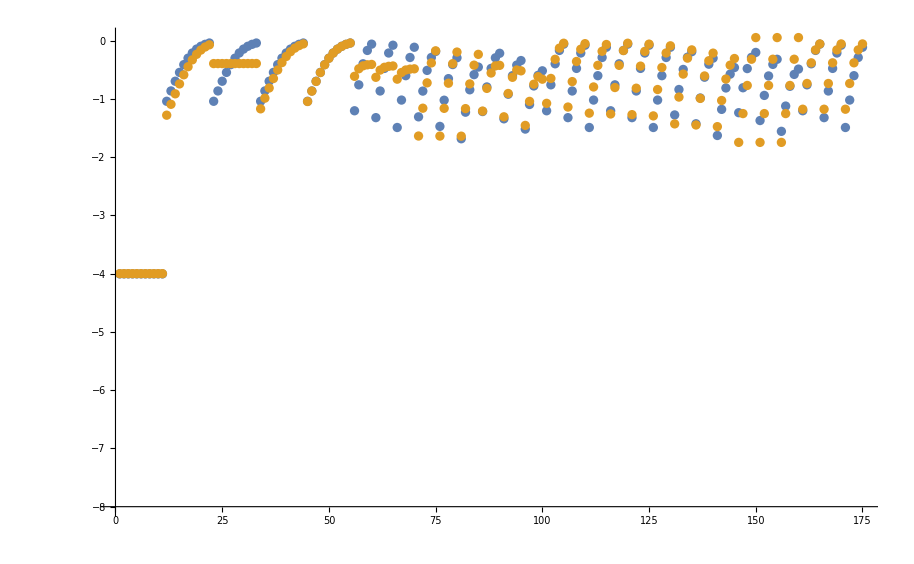

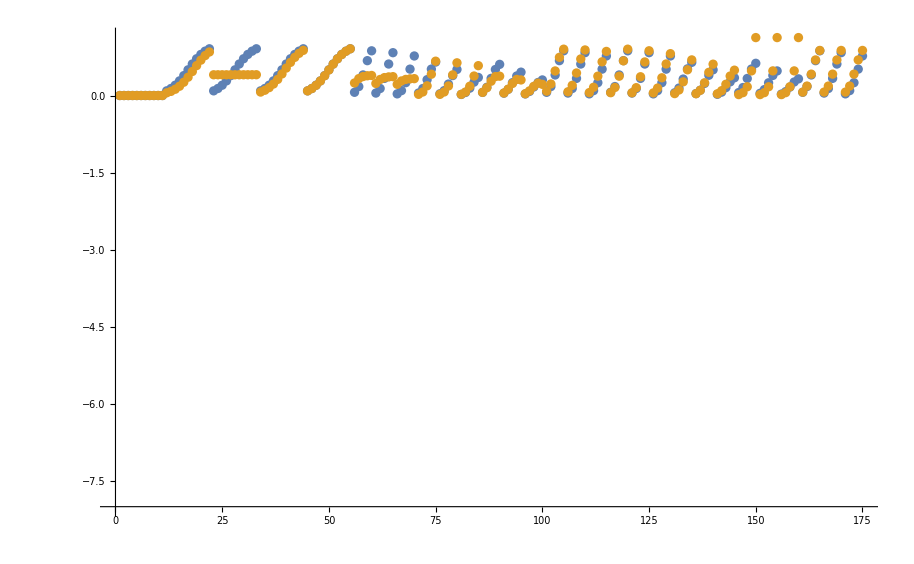

```mathematica
datasetI=1;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

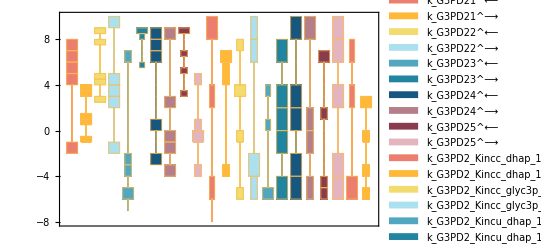

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

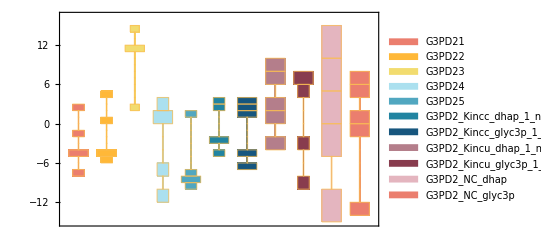

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

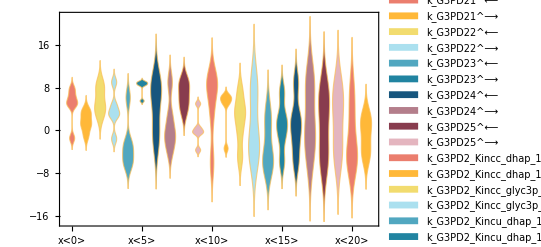

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

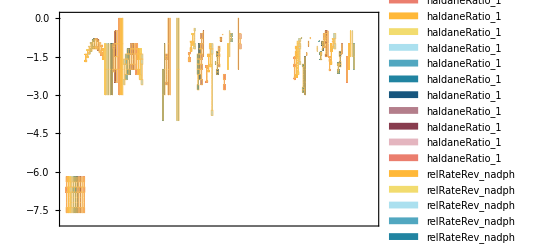

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
dataHeader = Import[dataFilePath][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse,metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

data value | predicted value | error in %
3.4×10^-6 | 6.14002×10^-6 | 80.5887
0.00018 | 0.161674 | 89718.9
0.000165 | 0.000228036 | 38.2039
0.00003 | 0.0000302847 | 0.948941

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1,3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.000099 | 0.0000999654 | 0.975181

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.000099 | 0.0000999654 | 0.975181

```mathematica
backCalculateKic[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %
4.2×10^-6 | 0.00408399 | 97137.9
2.5×10^-6 | 0.00674614 | 269745.
0.0013 | 0.00179938 | 38.4136
0.000187 | 0.000449322 | 140.279
0.000038 | 0.00071685 | 1786.45
0.00012 | 0.00270153 | 2151.27
6.×10^-7 | 3.5104 | 5.85066×10^8
4.×10^-7 | 3.33576 | 8.33939×10^8

```mathematica
backCalculateKiu[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %
6.5×10^-6 | 0.0000302491 | 365.37
0.0013 | 0.00305859 | 135.276
0.00024 | 0.000481717 | 100.715
8.×10^-7 | 48.8981 | 6.11227×10^9

#### Export rate back calculated parameter error distribution

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

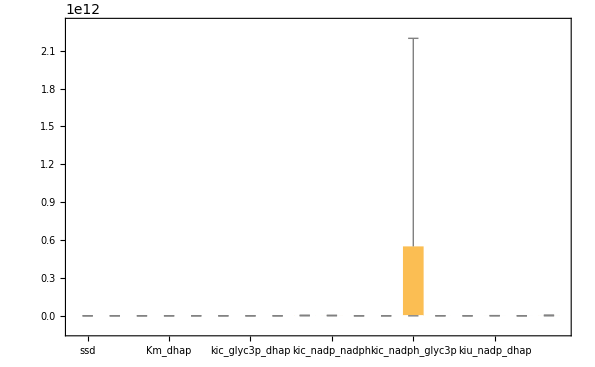

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```